# HW 3

### Shahaf Zohar - 205978000 Roey Salah - 206115438

Given a graph with 43 vertices and 293 arcs.Drop one arc from each node, our goal is to find the missing arcs

The removed arcs were removed randomly

#### To solve the problem One way simple approach is to use common . The idea is that if two nodes have many common neighbors, then they are likely to be connected by an edge.

Another way solve the problem One approach to finding the missing edges is to use a community detection algorithm to partition the graph into communities and then add edges between nodes in different communities .

```mathematica
edges ={1<->2,1<->4,1<->5,1<->6,1<->7,1<->8,1<->9,1<->11,1<->12,1<->13,1<->14,1<->15,1<->16,2<->3,2<->5,2<->6,2<->7,2<->8,2<->10,2<->11,2<->12,2<->14,2<->15,2<->17,2<->18,2<->19,2<->20,2<->21,2<->22,2<->24,2<->28,2<->29,2<->30,2<->31,2<->32,2<->33,3<->4,3<->6,3<->7,3<->8,3<->9,3<->10,3<->11,3<->12,3<->14,3<->15,3<->16,3<->17,3<->18,3<->19,3<->20,3<->23,3<->24,3<->26,3<->27,3<->28,3<->32,3<->33,3<->34,3<->35,3<->36,3<->37,4<->5,4<->6,4<->10,4<->13,4<->14,4<->15,4<->17,4<->18,4<->20,4<->29,4<->32,4<->33,4<->35,5<->6,5<->8,5<->10,5<->11,5<->12,5<->18,5<->19,5<->20,5<->22,5<->23,5<->24,5<->25,5<->27,5<->28,5<->29,5<->30,5<->32,5<->33,6<->15,6<->19,6<->20,6<->21,6<->31,7<->8,7<->9,7<->10,7<->11,7<->12,7<->13,7<->16,7<->19,7<->24,7<->28,7<->29,7<->32,7<->34,7<->35,7<->36,7<->37,7<->38,7<->39,7<->41,7<->43,8<->9,8<->10,8<->11,8<->12,8<->14,8<->16,8<->18,8<->19,8<->22,8<->25,8<->28,8<->32,8<->35,8<->36,8<->38,9<->10,9<->11,9<->12,9<->13,9<->16,9<->28,9<->29,9<->30,9<->31,9<->32,9<->35,9<->36,9<->38,9<->39,9<->41,9<->42,9<->43,10<->11,10<->12,10<->14,10<->15,10<->16,10<->19,10<->20,10<->22,10<->23,10<->28,10<->29,10<->30,10<->32,10<->35,10<->36,10<->38,11<->12,11<->13,11<->14,11<->21,11<->25,11<->29,11<->30,11<->32,11<->35,11<->37,11<->38,11<->40,11<->43,12<->13,12<->14,12<->16,12<->19,12<->22,12<->33,12<->38,13<->16,13<->18,13<->35,13<->36,13<->43,14<->15,14<->19,14<->20,14<->22,14<->24,14<->26,14<->27,14<->33,15<->19,15<->20,15<->22,15<->33,16<->19,16<->28,16<->35,16<->36,16<->38,16<->43,17<->20,17<->21,18<->19,18<->20,18<->22,18<->23,18<->25,19<->20,19<->21,19<->22,19<->24,19<->30,19<->31,19<->32,19<->33,19<->35,19<->36,19<->38,20<->21,20<->22,20<->28,20<->29,20<->33,20<->42,21<->22,21<->32,22<->23,22<->26,22<->27,22<->28,24<->25,25<->32,26<->27,26<->28,28<->29,29<->30,29<->31,29<->35,29<->36,29<->38,29<->39,29<->41,29<->42,30<->31,30<->32,30<->41,30<->42,31<->32,31<->33,31<->34,31<->35,31<->36,31<->38,31<->39,31<->41,31<->43,32<->35,32<->36,32<->41,32<->42,34<->35,34<->36,34<->37,34<->38,34<->43,35<->37,35<->38,36<->37,36<->38,36<->39,36<->41,36<->42,36<->43,38<->39,38<->40,38<->42,38<->43,39<->40,39<->41,39<->42,40<->41,40<->42,40<->43,41<->42};
```

```mathematica
weights ={2,1,2,1,1,1,1,1,2,1,1,1,1,47,29,2,1,5,4,3,6,11,7,2,12,17,5,1,8,3,3,1,1,2,2,8,17,5,2,3,2,8,3,5,18,10,2,2,10,28,17,1,5,3,6,5,3,17,1,1,1,1,14,2,2,1,2,1,1,1,4,1,1,6,1,5,2,13,1,1,6,20,8,1,1,1,1,2,2,2,2,1,16,1,7,1,2,1,2,2,2,4,1,2,1,1,1,1,6,1,1,2,3,1,2,2,2,1,2,3,4,1,2,1,1,2,1,3,2,4,1,1,1,1,4,1,3,3,2,1,1,1,1,3,2,4,4,1,1,7,1,1,2,1,1,5,2,1,1,2,3,1,1,1,1,1,2,2,1,1,1,1,2,8,3,2,6,1,6,1,2,1,4,1,1,1,2,1,2,2,2,2,5,2,4,1,1,1,1,2,2,1,7,1,1,2,2,2,2,2,1,18,1,1,3,1,9,4,7,1,1,2,1,4,2,2,1,1,7,3,2,2,1,2,1,1,2,1,3,1,1,1,1,1,5,4,5,5,3,2,5,4,6,9,2,1,6,1,1,4,2,1,1,2,1,2,2,2,1,9,8,1,6,6,1,15,1,13,1,1,1,10,4,4,1,17,3,4,3,2,1,1,4};
```

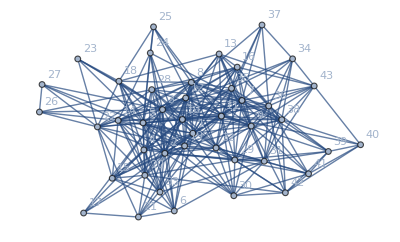

```mathematica
G =Graph[Range[43],edges, EdgeWeight->weights,VertexLabels->"Name"]
```

```mathematica
EdgeList[G];
```

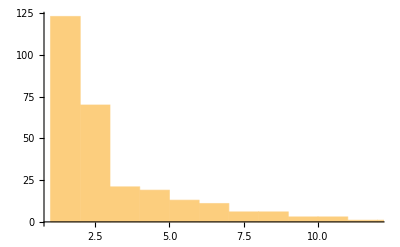

```mathematica
Histogram[PropertyValue[{G,#},EdgeWeight]&/@ EdgeList[G]]
```

```mathematica
VertexCount[G]
```

43

```mathematica
EdgeCount[G]
```

293

```mathematica
WeightsOfMissingEdges = {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,4,4,5,7,7,12,15,16,22,38};
```

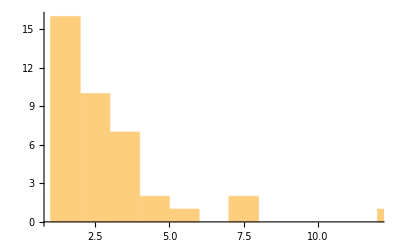

```mathematica
Histogram[WeightsOfMissingEdges]
```

```mathematica
missing = {{1<->3},{2<->27},{3<->5},{2<->4},{5<->14},{6<->10},{7<->42},{8<->43},{9<->34},{1<->10}};
```

```mathematica
ALGORITEM
```

```mathematica
missingEdges={};
For[i=1,i<=43,i++,neighbors1=VertexList[NeighborhoodGraph[G,i]];
For[j=i+1,j<=43,j++,neighbors2=VertexList[NeighborhoodGraph[G,j]];
common=Intersection[neighbors1,neighbors2];
If[Length[common]>=2&&!EdgeQ[G,i<->j],AppendTo[missingEdges,{i,j}];]]]
```

```mathematica
num = Length[missingEdges]
```

454

```mathematica
temp2={};
temp={};
For[j=1,j<=43,j++,AppendTo[temp,{}]];
For[j=1,j<=num,j++,AppendTo[temp[[missingEdges[[j]][[1]]]],missingEdges[[j]][[2]]]]
For[j=1,j<=num,j++,AppendTo[temp[[missingEdges[[j]][[2]]]],missingEdges[[j]][[1]]]]
temp2={};
For[j=11,j<=43,j++,AppendTo[temp2,{j}]];
For[i=11,i<=43,i++,
subsets=Select[Subsets[temp[[i]],{2}],Length[Union[#]]==2&];
AppendTo[temp2[[i-10]],RandomChoice[subsets,1]];
]
```

```mathematica
result={}
For[i=11,i<=43,i++,
AppendTo[result,{i,temp2[[i-10]][[2]][[1]][[1]],temp2[[i-10]][[2]][[1]][[2]]}]]
result
```

{{11,15,4},{12,28,41},{13,38,41},{14,23,30},{15,29,8},{16,33,14},{17,1,6},{18,36,14},{19,28,39},{20,32,16},{21,33,15},{22,25,9},{23,33,8},{24,31,33},{25,28,1},{26,5,24},{27,10,11},{28,4,13},{29,34,13},{30,40,21},{31,7,14},{32,15,29},{33,35,16},{34,2,8},{35,39,1},{36,2,15},{37,13,14},{38,14,30},{39,2,16},{40,30,31},{41,16,38},{42,8,34},{43,3,29}}

```mathematica
Export["205978000_206115438.csv",result,"CSV"]
```

205978000_206115438.csv